```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ClearSystemCache[];
```

## Definitions

```mathematica
kT=k1+k2+k3;
e2=k1×k2+k2×k3+k3×k1;
e3=k1×k2×k3;
```

```mathematica
K1=kT;
K2=e2^(1/2);
K3=e3^(1/3);
```

```mathematica
bisp=(24 K3^6-8 K2^2 K3^3 K1-8 K2^4 K1^2+22 K3^3 K1^3-6 K2^2 K1^4+2 K1^6)/(K1^3 K3^9);
```

```mathematica
bisp=(24 e3^2-8e2 e3 kT-8 e2^2 kT^2+22e3 kT^3-6e2 kT^4+2 kT^6)/(kT^3 e3);
```

```mathematica
shape=bisp(*×e3^2*);
```

```mathematica
S[x1_,x2_]=(Simplify[shape/.{k1->x1×k3,k2->x2×k3}]);
```

```mathematica
norm=S[1,1]
```

-34/9

```mathematica
toplotπdotdπ2[{x1_,x2_}]=S[x1,x2]/norm//Simplify
```

-1/(17 x1 x2 (1+x1+x2)^3)9 (x1^6+3 x1^5 (1+x2)-x1^4 (1-6 x2+x2^2)+(-1+x2^2)^2 (1+3 x2+x2^2)+3 x1 (-1+x2)^2 (1+4 x2+4 x2^2+x2^3)-3 x1^3 (2+3 x2+3 x2^2+2 x2^3)-x1^2 (1+9 x2+12 x2^2+9 x2^3+x2^4))

Export[NotebookDirectory[] <> "dotpinablapisquared.txt", toplotπdotdπ2[{x1, x2}]];

```mathematica
thing=(k1/k2+k1/k3+k2/k1+k2/k3+k3/k1+k3/k2)-(k1^2/(k2×k3)+k2^2/(k1×k3)+k3^2/(k1×k2))-2;
```

```mathematica
S[x1_,x2_]=(Simplify[thing/.{k1->x1×k3,k2->x2×k3}]);
```

```mathematica
norm=S[1,1]
```

1

```mathematica
toplotequil[{x1_,x2_}]=S[x1,x2]/norm//Simplify
```

(-x1^3+x1 (-1+x2)^2+x1^2 (1+x2)-(-1+x2)^2 (1+x2))/(x1 x2)

```mathematica
thing=(k1×k2×k3)/(k1+k2+k3)^3;
```

```mathematica
S[x1_,x2_]=(Simplify[thing/.{k1->x1×k3,k2->x2×k3}]);
```

```mathematica
norm=S[1,1]
```

1/27

```mathematica
toplotπdotcubed[{x1_,x2_}]=S[x1,x2]/norm//Simplify
```

(27 x1 x2)/(1+x1+x2)^3

```mathematica
p=27/(-21+743/(7×(20 π^2-193)));
Δ=(kT-2k1)(kT-2k2)(kT-2k3);
Γ=2/3 e2-1/3(k1^2+k2^2+k3^2);
```

```mathematica
thing=((1+p)Δ/e3^3-p×Γ^3/e3^4)×e3^2;
```

```mathematica
S[x1_,x2_]=(Simplify[thing/.{k1->x1×k3,k2->x2×k3}]);
```

```mathematica
norm=S[1,1]
```

(-7363+840 π^2-189 (-193+20 π^2))/(29114-2940 π^2)

```mathematica
toplotortho[{x1_,x2_}]=S[x1,x2]/norm//Simplify
```

(-((-7363+840 π^2) x1 (-1+x1-x2) (1+x1-x2) x2 (-1+x1+x2))+7 (-193+20 π^2) (x1^2+(-1+x2)^2-2 x1 (1+x2))^3)/((29114-2940 π^2) x1^2 x2^2)

Export[NotebookDirectory[] <> "orthogonal.txt", toplotortho[{x1, x2}]];

## Region and cosine definitions

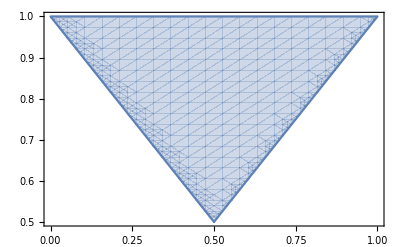

```mathematica
RegionPlot[x2>Abs[x1-1]&&x1<x2,{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio]
```

```mathematica
dot[S1_,S2_]:=NIntegrate[S1[{x1,x2}]S2[{x1,x2}]Boole[x2>Abs[x1-1]&&x1<x2],{x1,0,1},{x2,1/2,1}];
cos[S1_,S2_]:=dot[S1,S2]/Sqrt[dot[S1,S1]dot[S2,S2]];
```

I have that the single-field bispectrum is f_(NL,(π̇(∇π))^2)B_((π̇(∇π))^2)+f_(NL,(π̇)^3)B_((π̇)^3). I can also write it as f_(NL,equil.)B_(equil.)+f_(NL,ortho.)B_(ortho.) -> suppose I write B_((π̇(∇π))^2)=Cos[θ]B_(equil.)+Sin[θ]B_(ortho.), and with an angle φ for the other (notice that equil. and ortho. are orthonormal) -> what happens? I can relate the f_NL by some matrices of scalar products. That’s the point of Leonardo...

```mathematica
invM=Rationalize[({{dot[toplotequil,toplotπdotdπ2]/dot[toplotequil,toplotequil], dot[toplotequil,toplotπdotcubed]/dot[toplotequil,toplotequil]}, {dot[toplotortho,toplotπdotdπ2]/dot[toplotortho,toplotortho], dot[toplotortho,toplotπdotcubed]/dot[toplotortho,toplotortho]}}),10^-32]
```

{{513865931/494001065,227154851/187668044},{-18794399/475638518,-81528755/464062707}}

```mathematica
invM=N[invM,6]
```

{{1.04021,1.21041},{-0.039514,-0.175685}}

{{1.04021, 1.21041}, {-0.039514, -0.175685}}

```mathematica
invM=({{dot[toplotequil,toplotπdotdπ2]/dot[toplotequil,toplotequil], dot[toplotequil,toplotπdotcubed]/dot[toplotequil,toplotequil]}, {dot[toplotortho,toplotπdotdπ2]/dot[toplotortho,toplotortho], dot[toplotortho,toplotπdotcubed]/dot[toplotortho,toplotortho]}})
```

{{1.04021,1.21041},{-0.039514,-0.175685}}

```mathematica
invM.{1,0}
```

{1.04021,-0.039514}

```mathematica
invM.{0,1}
```

{1.21041,-0.175685}

```mathematica
dotpinablapisquaredcombo[{x1_,x2_}]=(invM.{1,0}).{toplotequil[{x1,x2}],toplotortho[{x1,x2}]}
```

(1.04021 (-x1^3+x1 (-1+x2)^2+x1^2 (1+x2)-(-1+x2)^2 (1+x2)))/(x1 x2)-(0.000405842 (-((-7363+840 π^2) x1 (-1+x1-x2) (1+x1-x2) x2 (-1+x1+x2))+7 (-193+20 π^2) (x1^2+(-1+x2)^2-2 x1 (1+x2))^3))/(x1^2 x2^2)

```mathematica
dotpinablapisquaredcombohelp[{x1_,x2_}]=(invM.{1,0}).{toplotequil[{x1,x2}],toplotortho[{x1,x2}]}
```

(1.04021 (-x1^3+x1 (-1+x2)^2+x1^2 (1+x2)-(-1+x2)^2 (1+x2)))/(x1 x2)-(0.000405842 (-((-7363+840 π^2) x1 (-1+x1-x2) (1+x1-x2) x2 (-1+x1+x2))+7 (-193+20 π^2) (x1^2+(-1+x2)^2-2 x1 (1+x2))^3))/(x1^2 x2^2)

```mathematica
dotpinablapisquaredcombo[{1,1}]
```

1.0007

```mathematica
dotpinablapisquaredcombo[{x1_,x2_}]=Rationalize[dotpinablapisquaredcombo[{x1,x2}]/dotpinablapisquaredcombo[{1,1}],10^-32]
```

(57003219 ((513865931 (-x1^3+x1 (-1+x2)^2+x1^2 (1+x2)-(-1+x2)^2 (1+x2)))/(494001065 x1 x2)-(686371 (-((-7363+840 π^2) x1 (-1+x1-x2) (1+x1-x2) x2 (-1+x1+x2))+7 (-193+20 π^2) (x1^2+(-1+x2)^2-2 x1 (1+x2))^3))/(1691226281 x1^2 x2^2)))/57043016

```mathematica
dotpicubedcombo[{x1_,x2_}]=(invM.{0,1}).{toplotequil[{x1,x2}],toplotortho[{x1,x2}]}
```

(1.21041 (-x1^3+x1 (-1+x2)^2+x1^2 (1+x2)-(-1+x2)^2 (1+x2)))/(x1 x2)-(0.00180443 (-((-7363+840 π^2) x1 (-1+x1-x2) (1+x1-x2) x2 (-1+x1+x2))+7 (-193+20 π^2) (x1^2+(-1+x2)^2-2 x1 (1+x2))^3))/(x1^2 x2^2)

```mathematica
dotpicubedcombo[{1,1}]
```

1.03472

```mathematica
dotpicubedcombo[{x1_,x2_}]=Rationalize[dotpicubedcombo[{x1,x2}]/dotpicubedcombo[{1,1}],10^-32]
```

(27828138 ((227154851 (-x1^3+x1 (-1+x2)^2+x1^2 (1+x2)-(-1+x2)^2 (1+x2)))/(187668044 x1 x2)-(2704802 (-((-7363+840 π^2) x1 (-1+x1-x2) (1+x1-x2) x2 (-1+x1+x2))+7 (-193+20 π^2) (x1^2+(-1+x2)^2-2 x1 (1+x2))^3))/(1498979025 x1^2 x2^2)))/28794413

(**)Export[NotebookDirectory[] <> "dotpinablapisquaredcombo.txt", dotpinablapisquaredcombo[{x1, x2}]];(**)
Export[NotebookDirectory[] <> "dotpicubedcombo.txt", dotpicubedcombo[{x1, x2}]];

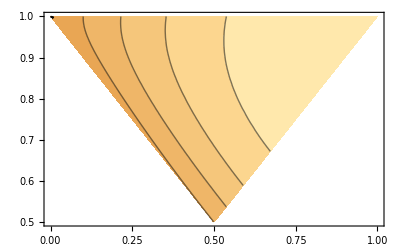

```mathematica
ContourPlot[dotpinablapisquaredcombo[{x1,x2}],{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio,RegionFunction->Function[{x1,x2,z},x2>Abs[x1-1]&&x1<x2],PlotRange->{-1,1}]
```

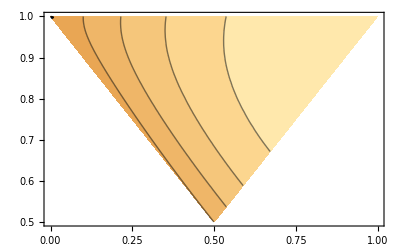

```mathematica
ContourPlot[toplotπdotdπ2[{x1,x2}],{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio,RegionFunction->Function[{x1,x2,z},x2>Abs[x1-1]&&x1<x2],PlotRange->{-1,1}]
```

```mathematica
(* I had made a mistake in the plots for ORTHOGONAL, this plot above shows that I did not make any mistake in saying that the combination for the π̇(∇π)^2 operator is essentially indistinguishable from the others. It still pays to do the plot though... *)
```

```mathematica
cos[toplotπdotdπ2,dotpinablapisquaredcombo]
```

1.

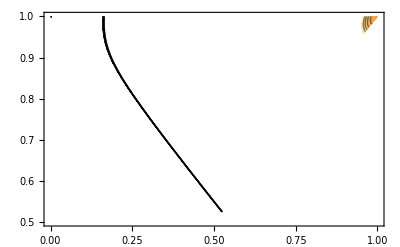

```mathematica
ContourPlot[toplotπdotdπ2[{x1,x2}]-dotpinablapisquaredcombo[{x1,x2}],{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio,RegionFunction->Function[{x1,x2,z},x2>Abs[x1-1]&&x1<x2],PlotRange->{-10^-5,10^-5}]
```

```mathematica
(* Marko: do relative-difference 1D plots! *)
```

x1=0.4;
Plot[(S[x1,x2,1]-Seft1[x1,x2,1])/Seft1[x1,x2,1],{x2,1-x1,1},PlotRange→All]

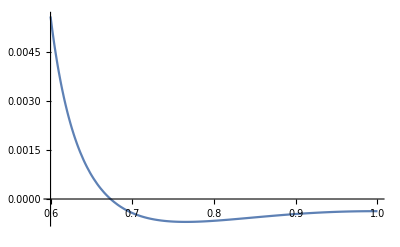

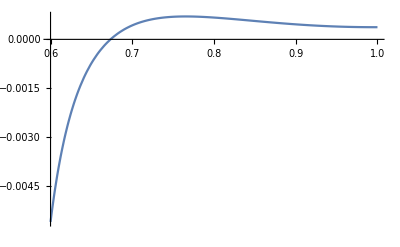

```mathematica
With[{x1=0.4},Plot[(toplotπdotdπ2[{x1,x2}]-dotpinablapisquaredcombohelp[{x1,x2}])/toplotπdotdπ2[{x1,x2}],{x2,1-x1,1},PlotRange->All]]
```

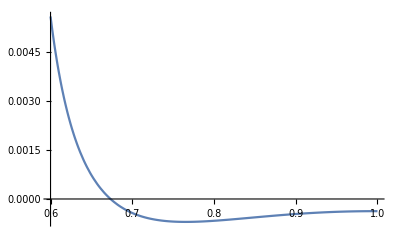

```mathematica
With[{x1=0.4},Plot[-((toplotπdotdπ2[{x1,x2}]-dotpinablapisquaredcombohelp[{x1,x2}])/toplotπdotdπ2[{x1,x2}]),{x2,1-x1,1},PlotRange->All]]
```

```mathematica
(* ok, there was a difference if I use my version rationalized... Interesting. Notice that, however, I do NOT send ANY of these results to Misha. I only send the matrix with a very low number of significant digits. Marko's code finds the EXACT SAME MATRIX AS ME. ***Only*** thing is -0.0395140, while he has -0.0395142... Whatever. I wrote him and he laughed, essentially... *)
```

x1=0.7;
Plot[(S[x1,x2,1]-Seft1[x1,x2,1])/Seft1[x1,x2,1],{x2,x1,1},PlotRange→All]

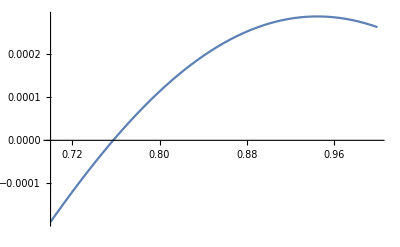

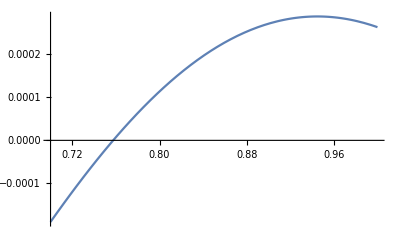

```mathematica
With[{x1=0.7},Plot[-((toplotπdotdπ2[{x1,x2}]-dotpinablapisquaredcombohelp[{x1,x2}])/toplotπdotdπ2[{x1,x2}]),{x2,x1,1},PlotRange->All]]
```

```mathematica
(* so these are essentially the same, I won't care to plot them in python... Now I have issues in plotting them. If we want to plot this, I can say the plot is essentially indistinguishable from the plot of the nonseparable shape of the operator with spatial derivatives... So one plots the two non-separable shapes, and then the separable orthogonal below... Which I indeed show to be very similar... *)
```

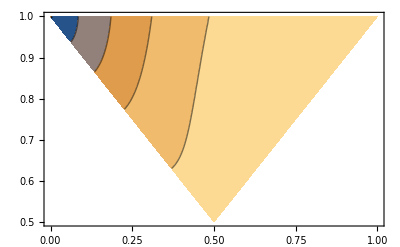

```mathematica
ContourPlot[dotpicubedcombo[{x1,x2}],{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio,RegionFunction->Function[{x1,x2,z},x2>Abs[x1-1]&&x1<x2]]
```

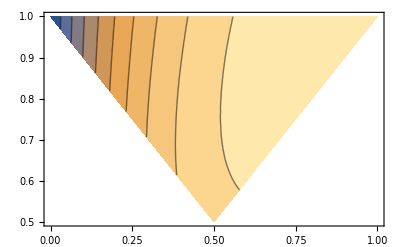

```mathematica
ContourPlot[toplotπdotcubed[{x1,x2}],{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio,RegionFunction->Function[{x1,x2,z},x2>Abs[x1-1]&&x1<x2]]
```

```mathematica
cos[toplotπdotcubed,dotpicubedcombo]
```

0.999507

```mathematica
(* perfect... Essentially total overlap... The constant-shape lines seem different? But I do not really know how they are computed, i.e. what the lines in the plots above are... Well, they are the lines of constant shape... *)
```

```mathematica
(* orthogonal... *)
```

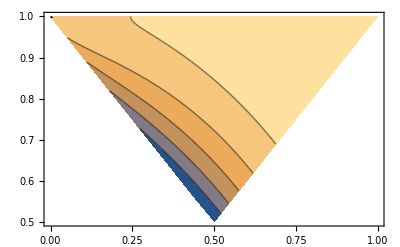

```mathematica
ContourPlot[toplotortho[{x1,x2}],{x1,0,1},{x2,1/2,1},AspectRatio->1/GoldenRatio,RegionFunction->Function[{x1,x2,z},x2>Abs[x1-1]&&x1<x2],PlotRange->{-5,1}]
```

```mathematica
(* check... *)
```

```mathematica
invM
```

{{1.04021,1.21041},{-0.039514,-0.175685}}

```mathematica
M=Inverse[invM]
```

{{1.30213,8.97121},{-0.292867,-7.70977}}

```mathematica
M.{fequil,fortho}
```

{1.30213 fequil+8.97121 fortho,-0.292867 fequil-7.70977 fortho}

```mathematica
invMLEO={{1.040,1.210},{0.1079,-0.06572}}
```

{{1.04,1.21},{0.1079,-0.06572}}

```mathematica
MatrixForm[invMLEO]
```

(1.04 | 1.21
0.1079 | -0.06572)

```mathematica
Inverse[invMLEO]
```

{{0.330404,6.08322},{0.542462,-5.22855}}